## Markov Partition and Symbolic Dynamics

### Initialization

```mathematica
M := {{1,1},{1,2}}
𝔉[{x_,y_}] := M.{x,y}
F[{x_,y_}]:= Mod[𝔉[{x,y}],1]
```

```mathematica
invM:=Inverse[M]
inv𝔉[{x_,y_}]:=invM.{x,y}
invF[{x_,y_}] := Mod[inv𝔉[{x,y}],1]
```

```mathematica
{eigenValue,eigenVector}=Eigensystem[M]
```

{{1/2 (3+√5),1/2 (3-√5)},{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}}

```mathematica
σDef:=σ->(3+Sqrt[5])/2
ϕDef:= ϕ->(1+Sqrt[5])/2
```

```mathematica
A1Def:=A1->Sqrt[(5-Sqrt[5])/10]
A2Def:=A2->Sqrt[50+22Sqrt[5]]/(5+Sqrt[5])
B1Def:=B1->Sqrt[1-2/Sqrt[5]]
B2Def:=B2->2Sqrt[5+2Sqrt[5]]/(5+Sqrt[5])
ABDef:={A1->Sqrt[(5-Sqrt[5])/10],A2->Sqrt[50+22Sqrt[5]]/(5+Sqrt[5]),B1->Sqrt[1-2/Sqrt[5]],B2->2Sqrt[5+2Sqrt[5]]/(5+Sqrt[5])}
```

```mathematica
vertexD={{{-ϕ/(1+ϕ^2),1/(1+ϕ^2)},{1/(1+ϕ^2),(1+ϕ+ϕ^2)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),-1+(2 ϕ (1+ϕ))/(1+ϕ^2)},{-1+(1+ϕ)/(1+ϕ^2),(-1+ϕ)/(1+ϕ^2)}},{{-1+(1+ϕ)/(1+ϕ^2),(-1+ϕ)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),-1+(2 ϕ (1+ϕ))/(1+ϕ^2)},{(1-ϕ+ϕ^2)/(1+ϕ^2),(2+ϕ^2)/(1+ϕ^2)},{(1-ϕ)/(1+ϕ^2),(2-ϕ)/(1+ϕ^2)}},{{(1-ϕ)/(1+ϕ^2),(2-ϕ)/(1+ϕ^2)},{(1-ϕ+ϕ^2)/(1+ϕ^2),(2+ϕ^2)/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{0,0}},{{1/(1+ϕ^2),ϕ/(1+ϕ^2)},{(1+ϕ)/(1+ϕ^2),(ϕ (1+ϕ))/(1+ϕ^2)},{-1+(2+3 ϕ)/(1+ϕ^2),(-2+2 ϕ+ϕ^2)/(1+ϕ^2)},{-1+(2 (1+ϕ))/(1+ϕ^2),(2 (-1+ϕ))/(1+ϕ^2)}},{{-1+(2 (1+ϕ))/(1+ϕ^2),(2 (-1+ϕ))/(1+ϕ^2)},{-1+(2+3 ϕ)/(1+ϕ^2),(-2+2 ϕ+ϕ^2)/(1+ϕ^2)},{1,1},{(1-ϕ+ϕ^2)/(1+ϕ^2),1/(1+ϕ^2)}}};
```

### Map Defined on the Partition

#### Preliminaries

The rotation that diagonalizes the cat matrix

```mathematica
eigenVector[[1]]
{{alpha,beta},{-beta,alpha}}.eigenVector[[1]]
Solve[{alpha+(1-ϕ/.ϕDef)beta==0,alpha^2+beta^2==1,alpha>0},{alpha,beta}]//Simplify
```

{1/2 (-1+√5),1}

{1/2 (-1+√5) alpha+beta,alpha-1/2 (-1+√5) beta}

{{alpha→-1/10 (-5+√5) √(1/2 (5+√5)),beta→√(1/10 (5+√5))}}

Useful identities.

```mathematica
αDef:=α->1/Sqrt[1+ϕ^2]
βDef:=β-> ϕ/Sqrt[1+ϕ^2]
αβDef:={α->1/Sqrt[1+ϕ^2],β-> ϕ/Sqrt[1+ϕ^2]}
```

```mathematica
R= {{α,β},{-β,α}};
Print["R = ",R//TraditionalForm]
```

R = (α | β
-β | α)

```mathematica
ArcCos[α]/.αDef/.ϕDef//N
```

1.01722

```mathematica
Print["R·R^T = ",R.Transpose[R]/.αβDef/.ϕDef//Simplify//TraditionalForm]
Print["R·M·R^T = ",R.M.Transpose[R]/.αβDef/.ϕDef//Simplify//TraditionalForm]
```

R·R^T = (1 | 0
0 | 1)

R·M·R^T = (1/2 (3+√5) | 0
0 | 1/2 (3-√5))

Useful identities.

```mathematica
{A1,A2,B1,B2}/.A1Def/.A2Def/.B1Def/.B2Def//N
{α,β}/.αβDef/.ϕDef//N
Print["A1 = α is ",(A1/.A1Def)==(α/.αDef/.ϕDef)//N]
Print["A2 = α + β is ",(A2/.A2Def)==((α+β)/.αβDef/.ϕDef)//N]
Print["B1 = β - α is ",(B1/.B1Def)==((β-α)/.αβDef/.ϕDef)//N]
Print["B2 = β is ",(B2/.B2Def)==(β/.βDef/.ϕDef)//N]
Print["A2 - B2 = α is ",((A2-B2)/.A2Def/.B2Def)==(α/.αDef/.ϕDef)//N]
Print["A2 + B2 = σ β is ",((A2+B2)/.A2Def/.B2Def)==((σ β)/.σDef/.βDef/.ϕDef) //N]
```

{0.525731,1.37638,0.32492,0.850651}

{0.525731,0.850651}

A1 = α is True

A2 = α + β is True

B1 = β - α is True

B2 = β is True

A2 - B2 = α is True

A2 + B2 = σ β is True

Useful identities.

```mathematica
{0,A2/σ,A2(1-1/σ),2 A2/σ,A2}/.A2Def/.σDef//N
{0,A1/σ,A1(1-1/σ),A1}/.A1Def/.σDef//N
{B2(1-1/σ),2B2(1-1/σ),B2(2-1/σ)}/.B2Def/.σDef//N
{-B1,-B1(1-1/σ),0}/.B1Def/.σDef//N
```

{0.,0.525731,0.850651,1.05146,1.37638}

{0.,0.200811,0.32492,0.525731}

{0.525731,1.05146,1.37638}

{-0.32492,-0.200811,0.}

```mathematica
Print["A_2/σ = A_1 = α is ",(A2/σ/.A2Def/.σDef)==(A1/.A1Def)==(α/.αDef/.ϕDef)//N]
Print["A_2(1 - 1/σ) = β is ",(A2(1-1/σ)/.A2Def/.σDef)==(β/.βDef/.ϕDef)//N]
Print["B_2(1 - 1/σ) = A_2/σ = A_1 = α is ",(B2(1-1/σ)/.B2Def/.σDef)==(A2/σ/.A2Def/.σDef)==(A1/.A1Def)==(α/.αDef/.ϕDef)//N]
Print["B_2(2 - 1/σ) = A_2 = α + β is ",(B2(2-1/σ)/.B2Def/.σDef)==(A2/.A2Def)==(α+β/.αβDef/.ϕDef)//N]
Print["A_1(1 - 1/σ) = B_1 = β - α is ",(A1(1-1/σ)/.A1Def/.σDef)==(B1/.B1Def)==(β-α/.αβDef/.ϕDef)//N]
Print["A_1/σ = B_1(1 - 1/σ) is ",(A1/σ/.A1Def/.σDef)==B1(1-1/σ)/.B1Def/.σDef//N]
```

A_2/σ = A_1 = α is True

A_2(1 - 1/σ) = β is True

B_2(1 - 1/σ) = A_2/σ = A_1 = α is True

B_2(2 - 1/σ) = A_2 = α + β is True

A_1(1 - 1/σ) = B_1 = β - α is True

A_1/σ = B_1(1 - 1/σ) is True

#### Rotated coordinates

The rotated coordinates u and v.

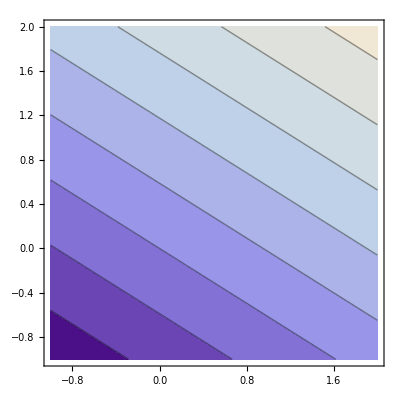

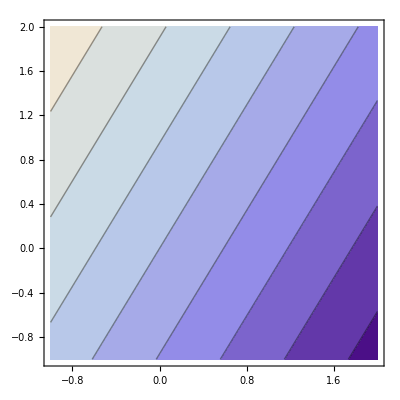

```mathematica
ContourPlot[(R.{x,y})[[1]]/.αβDef/.ϕDef//N,{x,-1,2},{y,-1,2}]
ContourPlot[(R.{x,y})[[2]]/.αβDef/.ϕDef//N,{x,-1,2},{y,-1,2}]
```

```mathematica
{x,y}-> Transpose[R].{u,v}
Cos[2Pi {kx,ky}.Transpose[R].{u,v}]
```

{x,y}→{u α-v β,v α+u β}

Cos[2 π (v (ky α-kx β)+u (kx α+ky β))]

```mathematica
{kx,ky}.Transpose[R]
R.{kx,ky}
%/.{kx->3,ky->-1}/.αβDef/.ϕDef
```

{kx α+ky β,ky α-kx β}

{kx α+ky β,ky α-kx β}

{3/(√(1+1/4 (1+√5)^2))-(1+√5)/(2 √(1+1/4 (1+√5)^2)),-1/(√(1+1/4 (1+√5)^2))-(3 (1+√5))/(2 √(1+1/4 (1+√5)^2))}

```mathematica
{A1,A2,B1,B2}/.ABDef//N
```

{0.525731,1.37638,0.32492,0.850651}

```mathematica
Cos[2Pi {kx,ky}.Transpose[R].{u,v}]/.αβDef/.ϕDef/.{u-> 0,v->0}
%//N//Expand
```

1

1.

```mathematica
Cos[2Pi {kx,ky}.Transpose[R].{u,v}]/.αβDef/.ϕDef/.{u-> A2/.A2Def,v->0}
%//N//Expand
%/.{kx->3,ky->-1}
```

Cos[(2 √(50+22 √5) (kx/(√(1+1/4 (1+√5)^2))+((1+√5) ky)/(2 √(1+1/4 (1+√5)^2))) π)/(5+√5)]

Cos[8.64806 (0.525731 kx+0.850651 ky)]

1.

```mathematica
Cos[2Pi {kx,ky}.Transpose[R].{u,v}]/.αβDef/.ϕDef/.{u-> 0,v->-A1/.A1Def}/.A2Def
%//N//Expand
%/.{kx->3,ky->-1}
```

Cos[√(2/5 (5-√5)) (-((1+√5) kx)/(2 √(1+1/4 (1+√5)^2))+ky/(√(1+1/4 (1+√5)^2))) π]

Cos[3.30327 (-0.850651 kx+0.525731 ky)]

-0.737369

```mathematica
Cos[2Pi {kx,ky}.Transpose[R].{u,v}]/.αβDef/.ϕDef/.{u-> 0,v->B1/.B1Def}/.A2Def
%//N//Expand
%/.{kx->3,ky->-1}
```

Cos[2 √(1-2/(√5)) (-((1+√5) kx)/(2 √(1+1/4 (1+√5)^2))+ky/(√(1+1/4 (1+√5)^2))) π]

Cos[2.04153 (-0.850651 kx+0.525731 ky)]

1.

#### Definition

The cells of the partition in the rotated coordinates.

```mathematica
isInDr[13,{u_,v_}]:=0≤ u<A1&& B1≤v<A1
isInDr[11,{u_,v_}]:=A1≤ u<2A1&&B1≤v<A1
isInDr[14,{u_,v_}]:=2A1≤ u<A2&& B1≤v<A1
isInDr[23,{u_,v_}]:=0≤ u<A1&&A1/σ≤v<B1
isInDr[21,{u_,v_}]:=A1≤ u<2A1&&A1/σ≤v<B1
isInDr[24,{u_,v_}]:=2A1≤ u<A2&& A1/σ≤v<B1
isInDr[33,{u_,v_}]:=0≤ u<A1&&0≤v<A1/σ
isInDr[31,{u_,v_}]:=A1≤ u<2A1&&0≤v<A1/σ
isInDr[34,{u_,v_}]:=2A1≤ u<A2&& 0≤v<A1/σ
isInDr[42,{u_,v_}]:=A1≤ u<2A1&&-A1/σ≤v<0
isInDr[45,{u_,v_}]:=2A1≤ u<A2&&-A1/σ≤v<0
isInDr[52,{u_,v_}]:=A1≤ u<2A1&&-B1≤v<-A1/σ
isInDr[55,{u_,v_}]:=2A1≤ u<A2&&-B1≤v<-A1/σ
```

The map in the rotated coordinates.

```mathematica
Fr[{u_,v_}]:=Piecewise[{
{{σ u,v/σ},isInDr[13,{u,v}]},
{{σ u-A2,v/σ+B1},isInDr[11,{u,v}]},
{{σ u-A2-B2,v/σ-A1/σ},isInDr[14,{u,v}]},
{{σ u,v/σ},isInDr[23,{u,v}]},
{{σ u-A2,v/σ+B1},isInDr[21,{u,v}]},
{{σ u-σ B2,v/σ-A1/σ},isInDr[24,{u,v}]},
{{σ u,v/σ},isInDr[33,{u,v}]},
{{σ u-A2,v/σ+B1},isInDr[31,{u,v}]},
{{σ u-σ B2,v/σ-A1/σ},isInDr[34,{u,v}]},
{{σ u-A2,v/σ+B1},isInDr[42,{u,v}]},
{{σ u-σ B2,v/σ-A1/σ},isInDr[45,{u,v}]},
{{σ u-A2,v/σ+B1},isInDr[52,{u,v}]},
{{σ u-σ B2,v/σ-A1/σ},isInDr[55,{u,v}]}
}]
```

The cells of the inverse map partition in the rotated coordinates.

```mathematica
isInDr[-13,{u_,v_}]:=0≤ u<A1&& B1≤v<A1
isInDr[-11,{u_,v_}]:=A1≤ u<2A1&&B1≤v<A1
isInDr[-14,{u_,v_}]:=2A1≤ u<A2&& B1≤v<A1
isInDr[-23,{u_,v_}]:=0≤ u<A1&&A1/σ≤v<B1
isInDr[-21,{u_,v_}]:=A1≤ u<2A1&&A1/σ≤v<B1
isInDr[-24,{u_,v_}]:=2A1≤ u<A2&& A1/σ≤v<B1
isInDr[-33,{u_,v_}]:=0≤ u<A1&&0≤v<A1/σ
isInDr[-31,{u_,v_}]:=A1≤ u<2A1&&0≤v<A1/σ
isInDr[-34,{u_,v_}]:=2A1≤ u<A2&& 0≤v<A1/σ
isInDr[-42,{u_,v_}]:=A1≤ u<2A1&&-A1/σ≤v<0
isInDr[-45,{u_,v_}]:=2A1≤ u<A2&&-A1/σ≤v<0
isInDr[-52,{u_,v_}]:=A1≤ u<2A1&&-B1≤v<-A1/σ
isInDr[-55,{u_,v_}]:=2A1≤ u<A2&&-B1≤v<-A1/σ
```

The inverse map in the rotated coordinates.

```mathematica
invFr[{u_,v_}]:=Piecewise[{
{{u/σ+A1,σ v-A1-B1},isInDr[-13,{u,v}]},
{{u/σ+A1,σ v-A1-B1},isInDr[-11,{u,v}]},
{{u/σ+A1,σ v-A1-B1},isInDr[-14,{u,v}]},
{{u/σ+A1,σ v-A1-B1},isInDr[-23,{u,v}]},
{{u/σ+A1,σ v-A1-B1},isInDr[-21,{u,v}]},
{{u/σ+A1,σ v-A1-B1},isInDr[-24,{u,v}]},
{{u/σ,σ v},isInDr[-33,{u,v}]},
{{u/σ,σ v},isInDr[-31,{u,v}]},
{{u/σ,σ v},isInDr[-34,{u,v}]},
{{u/σ+B2,σ v+A1},isInDr[-42,{u,v}]},
{{u/σ+B2,σ v+A1},isInDr[-45,{u,v}]},
{{u/σ+B2,σ v+A1},isInDr[-52,{u,v}]},
{{u/σ+B2,σ v+A1},isInDr[-55,{u,v}]}
}]
```

#### Periodic orbits in the rotated coordinates

The periodic orbits are no longer points with rational coordinates. One should stay in the original frame when studying periodic orbits.

```mathematica
X={0,3/5}
NestList[F,%,10]
NFr[{x_,y_}]:=Fr[{x,y}]/.ABDef/.σDef//N
(R/.αβDef/.ϕDef).X//N
NestList[NFr,%,10]
```

{0,3/5}

{{0,3/5},{3/5,1/5},{4/5,0},{4/5,4/5},{3/5,2/5},{0,2/5},{2/5,4/5},{1/5,0},{1/5,1/5},{2/5,3/5},{0,3/5}}

{0.51039,0.315439}

{{0.51039,0.315439},{1.33622,0.120487},{1.27124,-0.15479},{1.10111,-0.259936},{0.655699,-0.300098},{0.34026,0.210292},{0.890813,0.0803246},{0.955797,0.355601},{1.12593,0.460747},{0.720683,-0.0248217},{0.51039,0.315439}}

#### Boundary conditions on the fundamental domain in rotated coordinates

```mathematica
vertexDr=Map[R.#&,vertexD,{2}]/.αβDef/.ϕDef//N//Chop;
rotatedPartition=Graphics[{EdgeForm[Thick],Transparent,Polygon[#]}]&/@vertexDr;
range={{0,A2/.A2Def//N},{-B1/.B1Def//N,A1/.A1Def//N}};
aspect=(A1+B1)/A2/.ABDef//N;
side1=Graphics[{Thickness[0.02],Green,Line[{{A2,A1},{A2,A1-B1}}]}]/.ABDef//N;
side2=Graphics[{Thickness[0.02],Green,Line[{{A1,0},{A1,-B1}}]}]/.ABDef//N;
side3=Graphics[{Thickness[0.02],Yellow,Line[{{A2,A1-B1},{A2,-B1}}]}]/.ABDef//N;side4=Graphics[{Thickness[0.02],Yellow,Line[{{0,A1},{0,0}}]}]/.ABDef//N;
side5=Graphics[{Thickness[0.02],Blue,Line[{{0,A1},{B2,A1}}]}]/.ABDef//N;
side6=Graphics[{Thickness[0.02],Blue,Line[{{A1,-B1},{A2,-B1}}]}]/.ABDef//N;
side7=Graphics[{Thickness[0.02],Cyan,Line[{{B2,A1},{A2,A1}}]}]/.ABDef//N;
side8=Graphics[{Thickness[0.02],Cyan,Line[{{0,0},{A1,0}}]}]/.ABDef//N;
```

The five cells of the Markov partition with the boundary conditions on the fundamental domain in the rotated coordinates.

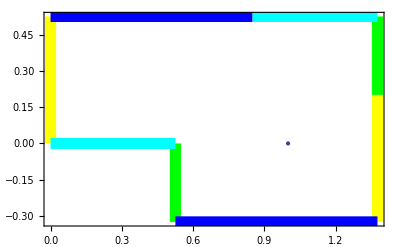

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
rotatedPartition,side1,side2,side3,side4,side5,side6,side7,side8, ImageSize->Scaled[0.75]]
```

```mathematica
vertexInvDr = {
{{0,0},{0,A1},{A1,A1},{A1,0}},
{{A1,0},{A1,A1},{2A1,A1},{2 A1,0}},
{{2 A1,0},{2 A1,A1},{A2,A1},{A2,0}},
{{A1,-B1},{A1,0},{2A1,0},{2 A1,-B1}},
{{2A1,-B1},{2A1,0},{A2,0},{A2,-B1}}
}/.ABDef/.σDef//N

rotatedInvPartition=Graphics[{EdgeForm[Thick],Transparent,Polygon[#]}]&/@vertexInvDr;
```

{{{0.,0.},{0.,0.525731},{0.525731,0.525731},{0.525731,0.}},{{0.525731,0.},{0.525731,0.525731},{1.05146,0.525731},{1.05146,0.}},{{1.05146,0.},{1.05146,0.525731},{1.37638,0.525731},{1.37638,0.}},{{0.525731,-0.32492},{0.525731,0.},{1.05146,0.},{1.05146,-0.32492}},{{1.05146,-0.32492},{1.05146,0.},{1.37638,0.},{1.37638,-0.32492}}}

The five cells of the Markov partition of the inverse map with the boundary conditions on the fundamental domain in the rotated coordinates.

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
rotatedInvPartition,side1,side2,side3,side4,side5,side6,side7,side8, ImageSize->Scaled[0.75]]
```

-Graphics-

```mathematica
(f[{0,v}]== f[{A2,v-B1}])/;0<v≤ A1 (* yellow *)
(f[{A1,v}]== f[{A2,v+A1}])/;-B1<v≤ 0 (* green *)
(f[{u,0}]==f[{u+B2,A1}])/;0<u≤ A1 (* cyan *)
(f[{u,A1}]==f[{u+A1,-B1}])/;0<u≤ B2 (* blue *)
```

f[{0,v}]==f[{A2,-B1+v}]/;0<v≤A1

f[{A1,v}]==f[{A2,A1+v}]/;-B1<v≤0

f[{u,0}]==f[{B2+u,A1}]/;0<u≤A1

f[{u,A1}]==f[{A1+u,-B1}]/;0<u≤B2

The boundary conditions of the fundamental domain on a function of u only.

```mathematica
fu[0]== fu[A2] (* yellow *)
fu[A1]== fu[A2] (* green *)
(f[u]==f[u+B2])/;0<u≤ A1 (* cyan *)
(f[u]==f[u+A1])/;0<u≤ B2 (* blue *)
```

fu[0]==fu[A2]

fu[A1]==fu[A2]

f[u]==f[B2+u]/;0<u≤A1

f[u]==f[A1+u]/;0<u≤B2

A function of u only will satisfy the boundary conditions only if it is invariant under two incommensurate translations which is not possible for a smooth function.

```mathematica
fu[0]== fu[A2] (* yellow *)
fu[A1]== fu[A2] (* green *)
(f[u]/;0<u≤ A1)==(f[u]/;B2<u≤ A2) (* cyan *)
(f[u]/;0<u≤ B2)==(f[u]/;A1<u≤ A2) (* blue *)
(f[u]/;0<u≤ B2-A1)==(f[u]/;A1<u≤ B2) (* blue *)
(f[u]/;0<u≤ A1)==(f[u]/;B2-A1<u≤ B2) (* cyan + blue *)
```

fu[0]==fu[A2]

fu[A1]==fu[A2]

(f[u]/;0<u≤A1)==(f[u]/;B2<u≤A2)

(f[u]/;0<u≤B2)==(f[u]/;A1<u≤A2)

(f[u]/;0<u≤B2-A1)==(f[u]/;A1<u≤B2)

(f[u]/;0<u≤A1)==(f[u]/;B2-A1<u≤B2)

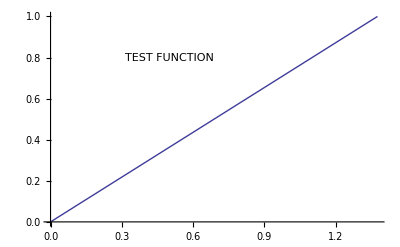

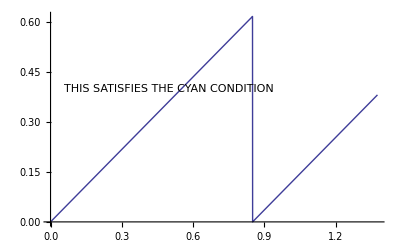

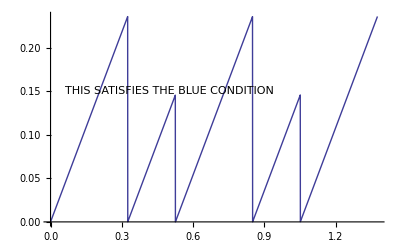

```mathematica
testFunction[u_]:=u/A2
Show[Plot[testFunction[u]/.ABDef//N,{u,0,A2/.ABDef//N}],Graphics@Text["TEST FUNCTION",{0.5,0.8}]]
B2testFunction[u_]:=Piecewise[{{testFunction[u],0<u≤ B2},{testFunction[u-B2]/.ABDef//N,B2<u≤ A2}}]
Show[Plot[B2testFunction[u]/.ABDef//N,{u,0,A2/.ABDef//N}],Graphics@Text["THIS SATISFIES THE CYAN CONDITION",{0.5,0.4}]]
A1testFunction[u_]:=Piecewise[{{testFunction[u],0<u≤ B2-A1},{testFunction[u-B2+A1],B2-A1<u≤ A1},{testFunction[u-A1],A1<u≤ B2}}]
Show[Plot[Piecewise[{{A1testFunction[u],0<u≤ B2},{A1testFunction[u-A1],A1<u≤ A2}}]/.ABDef//N,{u,0,A2/.ABDef//N}],Graphics@Text["THIS SATISFIES THE BLUE CONDITION",{0.5,0.15}]]
```

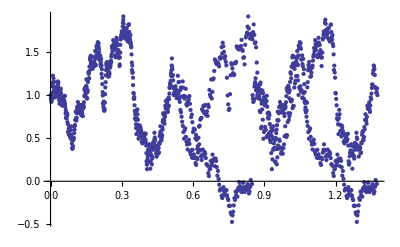

```mathematica
n=333;
domainA1=Table[A1 i/n,{i,0,n}]/.A1Def//N;
B2domainA1=domainA1+B2/.B2Def//N;
domainB2=Table[B2 i/n,{i,0,n}]/.B2Def//N;
A1domainB2=domainB2+A1/.A1Def//N;
domain=Join[domainA1,B2domainA1,domainB2,A1domainB2]//Sort//Union;
domain=Transpose[{Table[i,{i,Length[domain]}],domain}];
Clear[c];
boundaryConstrain=
Solve[Join[{
c[Position[domain,0.][[1,1]]]==
c[Position[domain,A2/.A2Def//N][[1,1]]],
c[Position[domain,A1/.A1Def//N][[1,1]]]==c[Position[domain,A2/.A2Def//N][[1,1]]]},
Table[c[Position[domain,domainA1[[i]]][[1,1]]]==c[Position[domain,B2domainA1[[i]]][[1,1]]],{i,Length[domainA1]}],
Table[c[Position[domain,domainB2[[i]]][[1,1]]]==c[Position[domain,A1domainB2[[i]]][[1,1]]],{i,Length[domainB2]}]
],
Table[c[i],{i,Length[domain]}]
];
independent = Table[boundaryConstrain[[1,i,2,1]],{i,Length[boundaryConstrain[[1]]]}]//Sort//Union;
ϵ=0.1;
span={-1,1};
c[independent[[1]]]=1;
Do[
c[independent[[i]]]=c[independent[[i-1]]]+ϵ RandomReal[span],
{i,2,Length[independent]}];
Table[c[i],{i,Length[domain]}]/.boundaryConstrain[[1]];
ListPlot[ { Table[domain[[i,2]],{i,Length[domain]}],Table[ c[i],{i,Length[domain]} ]/.boundaryConstrain [[1]]} //Transpose,PlotRange->Full, ImageSize->Scaled[1]]
```

#### Action of the map in the rotated coordinates

```mathematica
cellRandomPoints = Partition[Flatten[Table[{A2 RandomReal[1],(A1+B1) RandomReal[1]-B1}/.ABDef//N,{i, 0, 99}, {j,0, 99}]],2];
cellRandomPoints13=If[isInDr[13,#]/.ABDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints13WithHue={Blend[{Red,Yellow},0.5],Point[#]}&/@cellRandomPoints13;
cellRandomPoints11=If[isInDr[11,#]/.ABDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints11WithHue={Blend[{Red,Red},0.5],Point[#]}&/@cellRandomPoints11;
cellRandomPoints14=If[isInDr[14,#]/.ABDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints14WithHue={Blend[{Red,Green},0.5],Point[#]}&/@cellRandomPoints14;
cellRandomPoints23=If[isInDr[23,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints23WithHue={Blend[{Orange,Yellow},0.5],Point[#]}&/@cellRandomPoints23;
cellRandomPoints21=If[isInDr[21,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints21WithHue={Blend[{Orange,Red},0.5],Point[#]}&/@cellRandomPoints21;
cellRandomPoints24=If[isInDr[24,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints24WithHue={Blend[{Orange,Green},0.5],Point[#]}&/@cellRandomPoints24;
cellRandomPoints33=If[isInDr[33,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints33WithHue={Blend[{Yellow,Yellow},0.5],Point[#]}&/@cellRandomPoints33;
cellRandomPoints31=If[isInDr[31,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints31WithHue={Blend[{Yellow,Red},0.5],Point[#]}&/@cellRandomPoints31;
cellRandomPoints34=If[isInDr[34,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints34WithHue={Blend[{Yellow,Green},0.5],Point[#]}&/@cellRandomPoints34;
cellRandomPoints42=If[isInDr[42,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints42WithHue={Blend[{Green,Orange},0.5],Point[#]}&/@cellRandomPoints42;
cellRandomPoints45=If[isInDr[45,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints45WithHue={Blend[{Green,Blue},0.5],Point[#]}&/@cellRandomPoints45;
cellRandomPoints52=If[isInDr[52,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints52WithHue={Blend[{Blue,Orange},0.5],Point[#]}&/@cellRandomPoints52;
cellRandomPoints55=If[isInDr[55,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints55WithHue={Blend[{Blue,Blue},0.5],Point[#]}&/@cellRandomPoints55;
```

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPoints13WithHue,Graphics/@cellRandomPoints11WithHue,Graphics/@cellRandomPoints14WithHue,Graphics/@cellRandomPoints23WithHue,Graphics/@cellRandomPoints21WithHue,Graphics/@cellRandomPoints24WithHue,Graphics/@cellRandomPoints33WithHue,Graphics/@cellRandomPoints31WithHue,Graphics/@cellRandomPoints34WithHue,
Graphics/@cellRandomPoints42WithHue,Graphics/@cellRandomPoints45WithHue,
Graphics/@cellRandomPoints52WithHue,Graphics/@cellRandomPoints55WithHue,
rotatedPartition,Graphics[Text[Style["1.3","Title",Bold,Black],{0.3,0.42}]],Graphics[Text[Style["1.1","Title",Bold,Black],{0.8,0.42}]],Graphics[Text[Style["1.4","Title",Bold,Black],{1.2,0.42}]],Graphics[Text[Style["2.3","Title",Bold,Black],{0.3,0.25}]],Graphics[Text[Style["2.1","Title",Bold,Black],{0.8,0.25}]],Graphics[Text[Style["2.4","Title",Bold,Black],{1.2,0.25}]],Graphics[Text[Style["3.3","Title",Bold,Black],{0.3,0.1}]],Graphics[Text[Style["3.1","Title",Bold,Black],{0.8,0.1}]],Graphics[Text[Style["3.4","Title",Bold,Black],{1.2,0.1}]],Graphics[Text[Style["4.2","Title",Bold,Black],{0.8,-0.1}]],Graphics[Text[Style["4.5","Title",Bold,Black],{1.2,-0.1}]],Graphics[Text[Style["5.2","Title",Bold,Black],{0.8,-0.27}]],Graphics[Text[Style["5.5","Title",Bold,Black],{1.2,-0.27}]],side1,side2,side3,side4,side5,side6,side7,side8, ImageSize->Scaled[0.75]]
```

-Graphics-

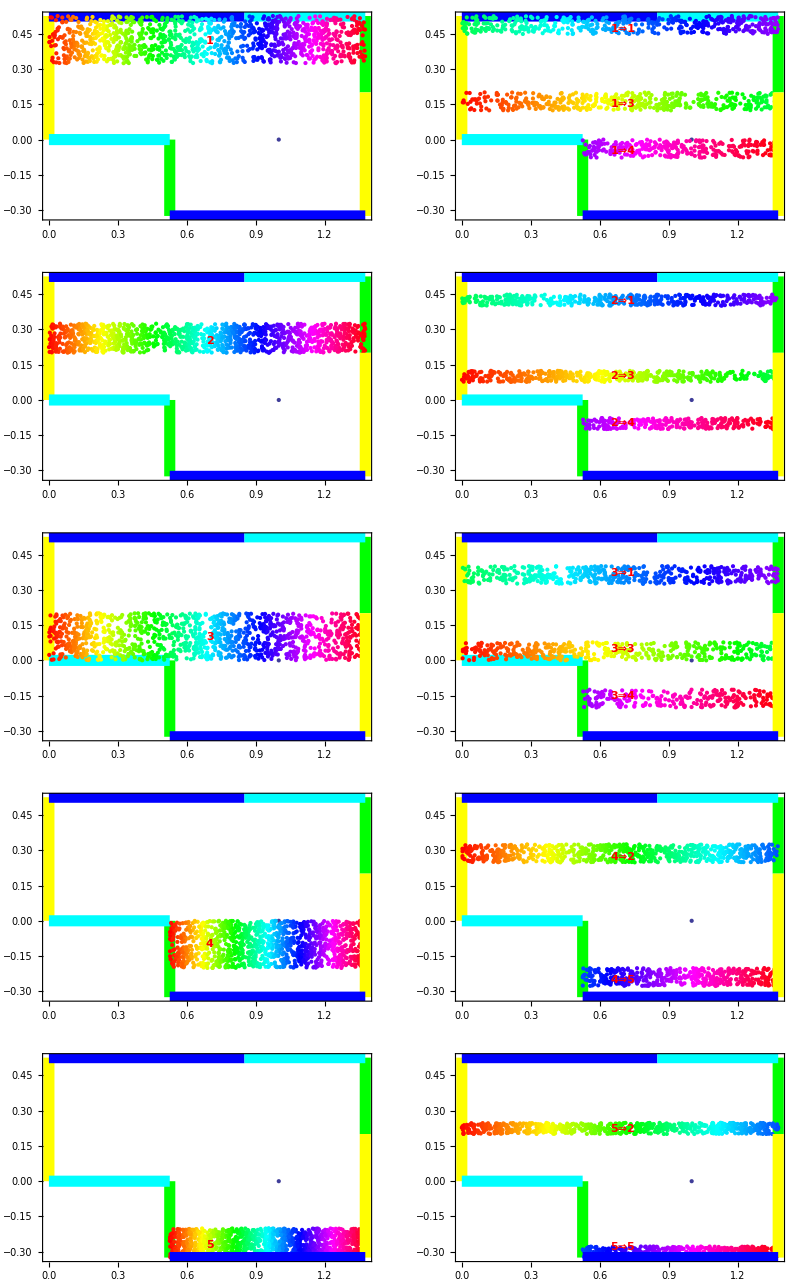

```mathematica
cellRandomPoints = Partition[Flatten[Table[{A2 RandomReal[1],(A1/σ) RandomReal[1]+A1(1-1/σ)}/.A1Def/.A2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[#[[1]]/A2/.A2Def//N],Point[#]}&/@cellRandomPoints;
g1=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics/@cellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["1","Title",Bold,Red],{0.7,0.42}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[Fr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g2=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics/@imageOfCellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["1⇒1","Title",Bold,Red],{0.7,0.47}]],Graphics[Text[Style["1⇒3","Title",Bold,Red],{0.7,0.15}]],Graphics[Text[Style["1⇒4","Title",Bold,Red],{0.7,-0.05}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = Partition[Flatten[Table[{A2 RandomReal[1],A1(1-2/σ) RandomReal[1]+A1/σ}/.A1Def/.A2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[#[[1]]/A2/.A2Def//N],Point[#]}&/@cellRandomPoints;
g3=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["2","Title",Bold,Red],{0.7,0.25}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[Fr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g4 = Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["2⇒1","Title",Bold,Red],{0.7,0.42}]],Graphics[Text[Style["2⇒3","Title",Bold,Red],{0.7,0.1}]],Graphics[Text[Style["2⇒4","Title",Bold,Red],{0.7,-0.1}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = 
Partition[
Flatten[
Table[{A2 RandomReal[1],(A1/σ) RandomReal[1]}/.A1Def/.A2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[#[[1]]/A2/.A2Def//N],Point[#]}&/@cellRandomPoints;
g5=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["3","Title",Bold,Red],{0.7,0.1}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[Fr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g6=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["3⇒1","Title",Bold,Red],{0.7,0.37}]],Graphics[Text[Style["3⇒3","Title",Bold,Red],{0.7,0.05}]],Graphics[Text[Style["3⇒4","Title",Bold,Red],{0.7,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = 
Partition[
Flatten[
Table[{B2 RandomReal[1]+B2(1-1/σ),B1(1-1/σ) (RandomReal[1]-1)}/.B1Def/.B2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[(#[[1]]-A1)/(A2-A1)/.ABDef//N],Point[#]}&/@cellRandomPoints;
g7=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio->aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["4","Title",Bold,Red],{0.7,-0.1}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[Fr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g8=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["4⇒2","Title",Bold,Red],{0.7,0.27}]],Graphics[Text[Style["4⇒5","Title",Bold,Red],{0.7,-0.25}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = 
Partition[
Flatten[
Table[{B2 RandomReal[1]+B2(1-1/σ),(B1/σ) RandomReal[1]-B1}/.B1Def/.B2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[(#[[1]]-A1)/(A2-A1)/.ABDef//N],Point[#]}&/@cellRandomPoints;
g9=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedPartition,rotatedPartition,Graphics[Text[Style["5","Title",Bold,Red],{0.7,-0.27}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[Fr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g10=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedPartition,Graphics[Text[Style["5⇒2","Title",Bold,Red],{0.7,0.22}]],Graphics[Text[Style["5⇒5","Title",Bold,Red],{0.7,-0.28}]],side1,side2,side3,side4,side5,side6,side7,side8];Show[GraphicsGrid[{{g1,g2},{g3,g4},{g5,g6},{g7,g8},{g9,g10}}],ImageSize->Scaled[1]]
```

#### Action of the inverse map in the rotated coordinates

```mathematica
cellRandomPoints = Partition[Flatten[Table[{A2 RandomReal[1],(A1+B1) RandomReal[1]-B1}/.ABDef//N,{i, 0, 99}, {j,0, 99}]],2];
cellRandomPoints13=If[isInDr[-13,#]/.ABDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints13WithHue={Blend[{Red,Yellow},0.5],Point[#]}&/@cellRandomPoints13;
cellRandomPoints11=If[isInDr[-11,#]/.ABDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints11WithHue={Blend[{Red,Red},0.5],Point[#]}&/@cellRandomPoints11;
cellRandomPoints14=If[isInDr[-14,#]/.ABDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints14WithHue={Blend[{Red,Green},0.5],Point[#]}&/@cellRandomPoints14;
cellRandomPoints23=If[isInDr[-23,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints23WithHue={Blend[{Orange,Yellow},0.5],Point[#]}&/@cellRandomPoints23;
cellRandomPoints21=If[isInDr[-21,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints21WithHue={Blend[{Orange,Red},0.5],Point[#]}&/@cellRandomPoints21;
cellRandomPoints24=If[isInDr[-24,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints24WithHue={Blend[{Orange,Green},0.5],Point[#]}&/@cellRandomPoints24;
cellRandomPoints33=If[isInDr[-33,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints33WithHue={Blend[{Yellow,Yellow},0.5],Point[#]}&/@cellRandomPoints33;
cellRandomPoints31=If[isInDr[-31,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints31WithHue={Blend[{Yellow,Red},0.5],Point[#]}&/@cellRandomPoints31;
cellRandomPoints34=If[isInDr[-34,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints34WithHue={Blend[{Yellow,Green},0.5],Point[#]}&/@cellRandomPoints34;
cellRandomPoints42=If[isInDr[-42,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints42WithHue={Blend[{Green,Orange},0.5],Point[#]}&/@cellRandomPoints42;
cellRandomPoints45=If[isInDr[-45,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints45WithHue={Blend[{Green,Blue},0.5],Point[#]}&/@cellRandomPoints45;
cellRandomPoints52=If[isInDr[-52,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints52WithHue={Blend[{Blue,Orange},0.5],Point[#]}&/@cellRandomPoints52;
cellRandomPoints55=If[isInDr[-55,#]/.ABDef/.σDef//N,#,{0,0}]&/@cellRandomPoints;
cellRandomPoints55WithHue={Blend[{Blue,Blue},0.5],Point[#]}&/@cellRandomPoints55;
```

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPoints13WithHue,Graphics/@cellRandomPoints11WithHue,Graphics/@cellRandomPoints14WithHue,Graphics/@cellRandomPoints23WithHue,Graphics/@cellRandomPoints21WithHue,Graphics/@cellRandomPoints24WithHue,Graphics/@cellRandomPoints33WithHue,Graphics/@cellRandomPoints31WithHue,Graphics/@cellRandomPoints34WithHue,
Graphics/@cellRandomPoints42WithHue,Graphics/@cellRandomPoints45WithHue,
Graphics/@cellRandomPoints52WithHue,Graphics/@cellRandomPoints55WithHue,
rotatedInvPartition,Graphics[Text[Style["1.3","Title",Bold,Black],{0.3,0.42}]],Graphics[Text[Style["1.1","Title",Bold,Black],{0.8,0.42}]],Graphics[Text[Style["1.4","Title",Bold,Black],{1.2,0.42}]],Graphics[Text[Style["2.3","Title",Bold,Black],{0.3,0.25}]],Graphics[Text[Style["2.1","Title",Bold,Black],{0.8,0.25}]],Graphics[Text[Style["2.4","Title",Bold,Black],{1.2,0.25}]],Graphics[Text[Style["3.3","Title",Bold,Black],{0.3,0.1}]],Graphics[Text[Style["3.1","Title",Bold,Black],{0.8,0.1}]],Graphics[Text[Style["3.4","Title",Bold,Black],{1.2,0.1}]],Graphics[Text[Style["4.2","Title",Bold,Black],{0.8,-0.1}]],Graphics[Text[Style["4.5","Title",Bold,Black],{1.2,-0.1}]],Graphics[Text[Style["5.2","Title",Bold,Black],{0.8,-0.27}]],Graphics[Text[Style["5.5","Title",Bold,Black],{1.2,-0.27}]],side1,side2,side3,side4,side5,side6,side7,side8,ImageSize->Scaled[0.75]]
```

-Graphics-

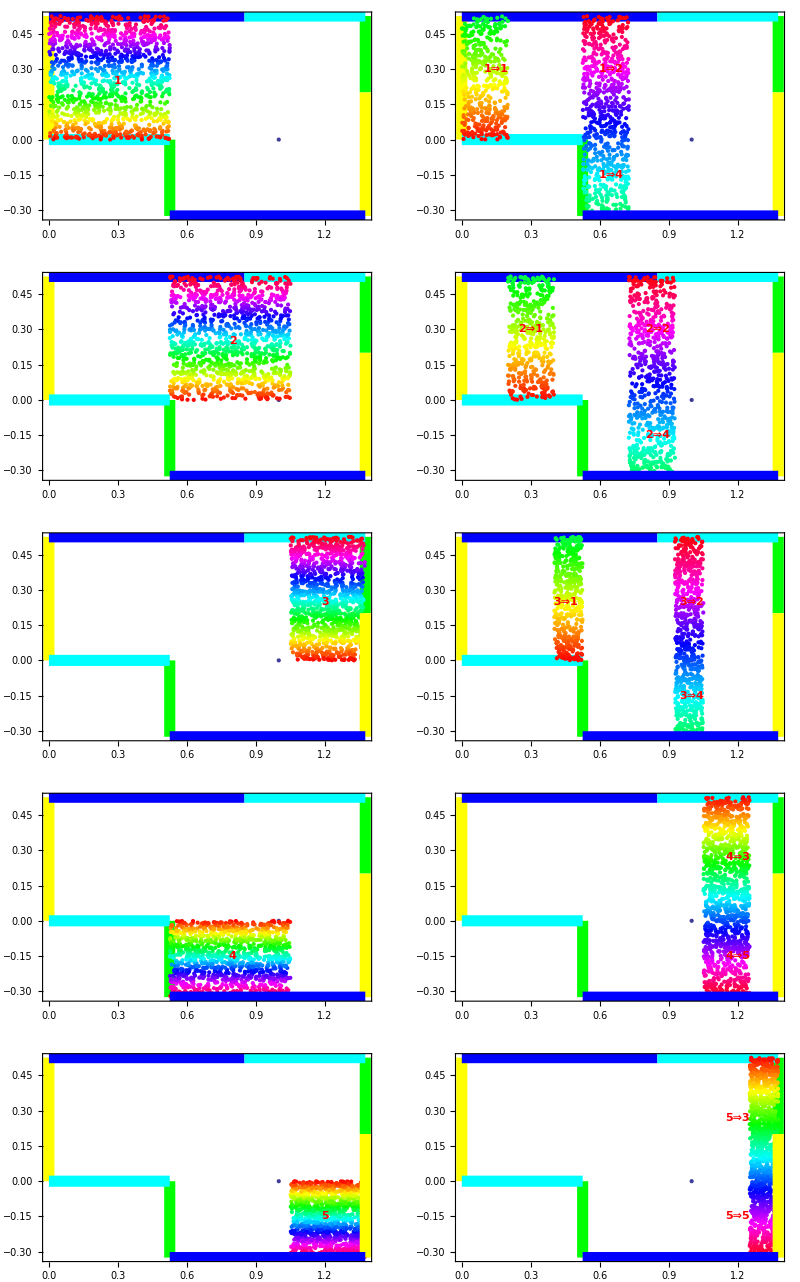

```mathematica
cellRandomPoints = Partition[Flatten[Table[{A1 RandomReal[1],A1 RandomReal[1]}/.A1Def/.A2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[#[[2]]/A1/.A1Def//N],Point[#]}&/@cellRandomPoints;
g1=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics/@cellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["1","Title",Bold,Red],{0.3,0.25}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[invFr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g2=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics/@imageOfCellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["1⇒1","Title",Bold,Red],{0.15,0.3}]],Graphics[Text[Style["1⇒2","Title",Bold,Red],{0.65,0.3}]],Graphics[Text[Style["1⇒4","Title",Bold,Red],{0.65,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = Partition[Flatten[Table[{A1 (RandomReal[1]+1),A1 RandomReal[1]}/.A1Def/.A2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[#[[2]]/A1/.A1Def//N],Point[#]}&/@cellRandomPoints;
g3=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["2","Title",Bold,Red],{0.8,0.25}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[invFr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g4=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["2⇒1","Title",Bold,Red],{0.3,0.3}]],Graphics[Text[Style["2⇒2","Title",Bold,Red],{0.85,0.3}]],Graphics[Text[Style["2⇒4","Title",Bold,Red],{0.85,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = 
Partition[
Flatten[
Table[{B1 RandomReal[1]+2A1,A1 RandomReal[1]}/.ABDef/.A2Def/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[#[[2]]/A1/.A1Def//N],Point[#]}&/@cellRandomPoints;
g5=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["3","Title",Bold,Red],{1.2,0.25}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[invFr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g6=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["3⇒1","Title",Bold,Red],{0.45,0.25}]],Graphics[Text[Style["3⇒2","Title",Bold,Red],{1.0,0.25}]],Graphics[Text[Style["3⇒4","Title",Bold,Red],{1.0,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = 
Partition[
Flatten[
Table[{A1 RandomReal[1]+A1,-B1 RandomReal[1]}/.ABDef/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[-#[[2]]/B1/.ABDef//N],Point[#]}&/@cellRandomPoints;
g7=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio->aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["4","Title",Bold,Red],{0.8,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[invFr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g8=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["4⇒3","Title",Bold,Red],{1.2,0.27}]],Graphics[Text[Style["4⇒5","Title",Bold,Red],{1.2,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
cellRandomPoints = 
Partition[
Flatten[
Table[{B1 RandomReal[1]+2A1,-B1 RandomReal[1]}/.ABDef/.σDef//N,{i, 0, 33}, {j,0, 33}]],2];
cellRandomPointsWithHue={Hue[-#[[2]]/B1/.ABDef//N],Point[#]}&/@cellRandomPoints;
g9=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@cellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["5","Title",Bold,Red],{1.2,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
imageOfCellRandomPointsWithHue = Map[{#[[1]],Point[invFr[#[[2,1]]]]}&,cellRandomPointsWithHue]/.ABDef/.ϕDef/.σDef//N;
g10=Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],Graphics/@imageOfCellRandomPointsWithHue,rotatedInvPartition,Graphics[Text[Style["5⇒3","Title",Bold,Red],{1.2,0.27}]],Graphics[Text[Style["5⇒5","Title",Bold,Red],{1.2,-0.15}]],side1,side2,side3,side4,side5,side6,side7,side8];
Show[GraphicsGrid[{{g1,g2},{g3,g4},{g5,g6},{g7,g8},{g9,g10}}],ImageSize->Scaled[1]]
```

#### Derivation of the u-Map

A smooth distribution under the iteration of the map (under the action of the Koopman operator) is folded more and more in the u direction and stretched more and more in the v direction. Asymptotically it becomes a highly irregular distribution that is a function of only u and that satisfies the boundary conditions as well.

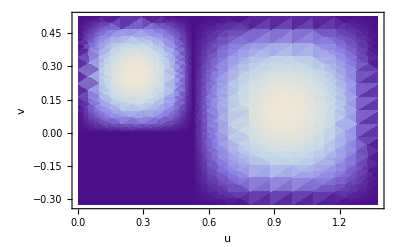

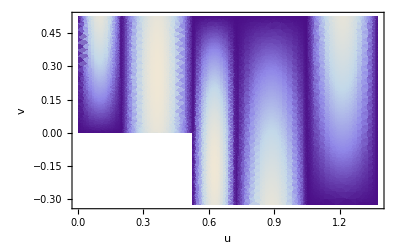

-Graphics-

-Graphics-

-Graphics-

```mathematica
testDistribution[{u_,v_}]:=If[u≥(A1/.A1Def//N ),(Sin[Pi (u-A1)/(A2-A1)]Sin[Pi (v+B1)/(A1+B1)])/.ABDef//N,0]+If[u<(A1/.A1Def//N )&& v≥ 0,(Sin[Pi u/A1]Sin[Pi v/A1])/.ABDef//N,0]

Show[DensityPlot[testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic,AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef//N,rotatedPartition]

K1testDistribution[{u_,v_}]:=testDistribution[Fr[{u,v}]/.ABDef/.σDef//N];

Show[DensityPlot[K1testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic ,AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]

K2testDistribution[{u_,v_}]:=testDistribution[Fr[Fr[{u,v}]/.ABDef/.σDef//N]/.ABDef/.σDef//N];

Show[DensityPlot[K2testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic, AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]

K3testDistribution[{u_,v_}]:=testDistribution[Fr[Fr[Fr[{u,v}]/.ABDef/.σDef//N]/.ABDef/.σDef//N]/.ABDef/.σDef//N];

Show[DensityPlot[K3testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic, AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]

K4testDistribution[{u_,v_}]:=testDistribution[Fr[Fr[Fr[Fr[{u,v}]/.ABDef/.σDef//N]/.ABDef/.σDef//N]/.ABDef/.σDef//N]/.ABDef/.σDef//N];

Show[DensityPlot[K4testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic,AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]
```

A smooth distribution under the iteration of the inverse map (under the action of the Perron-Frobenius-Ruelle operator) is folded more and more in the v direction and stretched more and more in the u direction. Asymptotically it becomes a highly irregular distribution that is a function of only v and that satisfies the boundary conditions as well.

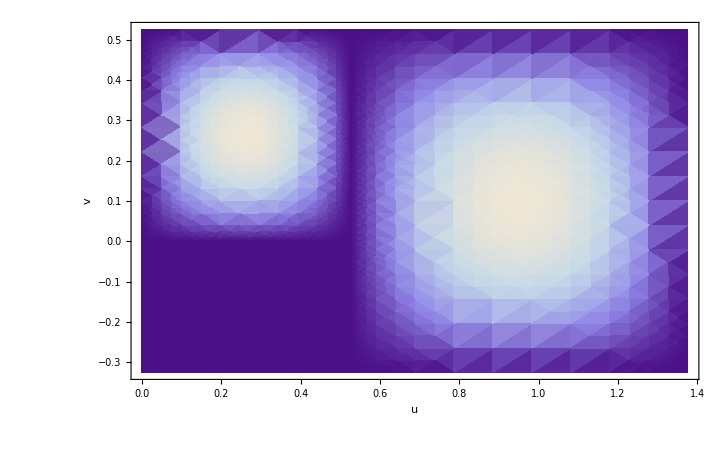

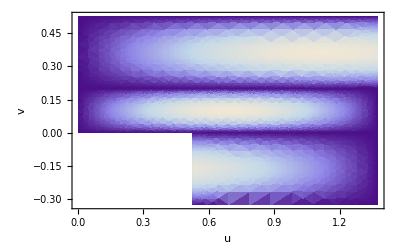

-Graphics-

-Graphics-

-Graphics-

```mathematica
testDistribution[{u_,v_}]:=If[u≥(A1/.A1Def//N ),(Sin[Pi (u-A1)/(A2-A1)]Sin[Pi (v+B1)/(A1+B1)])/.ABDef//N,0]+If[u<(A1/.A1Def//N )&& v≥ 0,(Sin[Pi u/A1]Sin[Pi v/A1])/.ABDef//N,0]

Show[DensityPlot[testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic,AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef//N,rotatedPartition]

L1testDistribution[{u_,v_}]:=testDistribution[invFr[{u,v}]/.ABDef/.σDef//N];

Show[DensityPlot[L1testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic ,AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]

L2testDistribution[{u_,v_}]:=testDistribution[invFr[invFr[{u,v}]/.ABDef/.σDef//N]/.ABDef/.σDef//N];

Show[DensityPlot[L2testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic, AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]

L3testDistribution[{u_,v_}]:=testDistribution[invFr[invFr[invFr[{u,v}]/.ABDef/.σDef//N]/.ABDef/.σDef//N]/.ABDef/.σDef//N];

Show[DensityPlot[L3testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic, AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]

L4testDistribution[{u_,v_}]:=testDistribution[invFr[invFr[invFr[invFr[{u,v}]/.ABDef/.σDef//N]/.ABDef/.σDef//N]/.ABDef/.σDef//N]/.ABDef/.σDef//N];

Show[DensityPlot[L4testDistribution[{u,v}], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel-> Automatic,AspectRatio->Automatic,Mesh->None,ExclusionsStyle->{None,Red},PerformanceGoal->"Quality",MaxRecursion->5]/.ABDef/.σDef//N,rotatedPartition]
```

```mathematica
vertexDr3D=Map[{#[[1]],#[[2]],0}&,vertexDr,{2}];
rotatedPartition3D=Graphics3D[{EdgeForm[Thick],Transparent,Polygon[#]}]&/@vertexDr3D;
ratios={A2,A1+B1,1}/.ABDef//N
```

{1.37638,0.850651,1.}

```mathematica
Show[{Plot3D[(Fr[{u,v}]/.ABDef/.σDef//N)[[1]], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75],AxesLabel->Automatic,PlotStyle->Directive[Red,Specularity[White,20],Opacity[0.8]]], rotatedPartition3D},BoxRatios->ratios]

Show[{Plot3D[(Fr[{u,v}]/.ABDef/.σDef//N)[[2]], {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75],AxesLabel->Automatic,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[0.8]]],rotatedPartition3D},BoxRatios->ratios]
```

Part::partd: Part specification 0. ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics3D-

Part::partd: Part specification 0. ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics3D-

The map can be factorized in a piecewise linear function of u to u and a piecewise linear function mapping (u,v) to v. Note that the Fu map is derived from the Arnold’s cat map. The one dimensional map studied by Hiroshi H. Hasegawa et al. is derived from the “square root” of the cat map and therefore it is a different map.

```mathematica
Fu[u_]:=Piecewise[{
{σ u,0≤ u<A1},
{σ u-A2,A1≤ u<2A1},
{σ u-A2-B2,2A1≤ u<A2}
}]
Fv[{u_,v_}]:=Piecewise[{
{v/σ,isInDr[13,{u,v}]},
{v/σ+B1,isInDr[11,{u,v}]},
{v/σ-A1/σ,isInDr[14,{u,v}]},
{v/σ,isInDr[23,{u,v}]},
{v/σ+B1,isInDr[21,{u,v}]},
{v/σ-A1/σ,isInDr[24,{u,v}]},
{v/σ,isInDr[33,{u,v}]},
{v/σ+B1,isInDr[31,{u,v}]},
{v/σ-A1/σ,isInDr[34,{u,v}]},
{v/σ+B1,isInDr[42,{u,v}]},
{v/σ-A1/σ,isInDr[45,{u,v}]},
{v/σ+B1,isInDr[52,{u,v}]},
{v/σ-A1/σ,isInDr[55,{u,v}]}
}]
```

```mathematica
Plot[Fu[u]/.ABDef/.σDef//N, {u,0,A2/.A2Def//N},Frame->True, ImageSize->Scaled[0.5], AspectRatio-> Automatic,PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[{Plot3D[Fv[{u,v}]/.ABDef/.σDef//N, {u,0,A2/.A2Def//N},{v,-B1/.B1Def//N,A1/.A1Def//N},ImageSize->Scaled[0.75], AxesLabel->Automatic,AspectRatio-> Automatic,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[0.8]]],rotatedPartition3D},BoxRatios->ratios]
```

-Graphics3D-

The partial derivative with respect to v of a distribution after n iterations of the map is the partial derivative of the distribution at the n-th iterated point times the product of the partial derivatives with respect to v of the v-map along the orbit up to the n-th iteration. This product is just σ^-n. This means that the norm of the partial derivative of the distribution with respect to v is multiplied by a factor of 1/σ at each map iteration.

```mathematica
D[f[gu[u],gv[u,v]],v]
D[f[gu[gu[u]],gv[gu[u],gv[u,v]]],v]
D[f[gu[gu[gu[u]]],gv[gu[gu[u]],gv[gu[u],gv[u,v]]]],v]
```

f^(0,1)[gu[u],gv[u,v]] gv^(0,1)[u,v]

f^(0,1)[gu[gu[u]],gv[gu[u],gv[u,v]]] gv^(0,1)[u,v] gv^(0,1)[gu[u],gv[u,v]]

f^(0,1)[gu[gu[gu[u]]],gv[gu[gu[u]],gv[gu[u],gv[u,v]]]] gv^(0,1)[u,v] gv^(0,1)[gu[u],gv[u,v]] gv^(0,1)[gu[gu[u]],gv[gu[u],gv[u,v]]]

Because the dependency on v of a distribution is washed out asymptotically as the map is iterated it makes sense to use a projection operator to get rid of the v dependency. Let’s define the projection operator that integrates out the dependency on v.

```mathematica
P[f_,u_]:=Piecewise[{{Integrate[f[{u,v}],{v,0,A1}]/A1,0≤ u<A1},{Integrate[f[{u,v}],{v,-B1,A1}]/(A1+B1),A1≤ u <A2}}/.ABDef]
```

```mathematica
P[fu[#[[1]]]#[[2]]^2&,u]
%//N
```

Piecewise[{{1/30 (5-√5) fu[u], 0≤u<√(1/10 (5-√5))}, {(1/3 (1-2/(√5))^(3/2) fu[u]+((5-√5)^(3/2) fu[u])/(30 √10))/(√(1-2/(√5))+√(1/10 (5-√5))), √(1/10 (5-√5))≤u<(√(50+22 √5))/(5+√5)}, {0, True}}]

Piecewise[{{0.0921311 fu[u], 0.≤u<0.525731}, {0.0703819 fu[u], 0.525731≤u<1.37638}, {0., True}}]

```mathematica
P[fu[#[[1]]]&,u]
%//N
```

Piecewise[{{fu[u], 0≤u<√(1/10 (5-√5))||√(1/10 (5-√5))≤u<(√(50+22 √5))/(5+√5)}, {0, True}}]

Piecewise[{{fu[u], 0.≤u<0.525731||0.525731≤u<1.37638}, {0., True}}]

The projection operator does not commute with the Koopman operator

```mathematica
PK[f_,u_]:=Piecewise[{{Integrate[f[{σ u,v/σ}],{v,0,A1}]/A1,0≤ u<A1},{Integrate[f[{σ u-A2,v/σ+B1}],{v,-B1,A1}]/(A1+B1),A1≤ u <2A1},{Integrate[f[{σ u-A2-B2,v/σ-A1/σ}],{v,-B1,A1}]/(A1+B1),2A1≤ u <A2}}/.ABDef/.σDef]
```

```mathematica
PK[fu[#[[1]]]#[[2]]^2&,u]
%//N
```

Piecewise[{{(2 (5-√5) fu[1/2 (3+√5) u])/(15 (3+√5)^2), 0≤u<√(1/10 (5-√5))}, {(4 (-(1-2/(√5))^(3/2) (-1+1/2 (3+√5))^3+(√(1/10 (5-√5))+1/2 √(1-2/(√5)) (3+√5))^3) fu[-(√(50+22 √5))/(5+√5)+1/2 (3+√5) u])/(3 (3+√5)^2 (√(1-2/(√5))+√(1/10 (5-√5)))), √(1/10 (5-√5))≤u<√(2/5 (5-√5))}, {(4 (√(1-2/(√5))+√(1/10 (5-√5)))^2 fu[-(2 √(5+2 √5))/(5+√5)-(√(50+22 √5))/(5+√5)+1/2 (3+√5) u])/(3 (3+√5)^2), √(2/5 (5-√5))≤u<(√(50+22 √5))/(5+√5)}, {0, True}}]

Piecewise[{{0.0134417 fu[2.61803 u], 0.≤u<0.525731}, {0.140764 fu[-1.37638+2.61803 u], 0.525731≤u<1.05146}, {0.0351909 fu[-2.22703+2.61803 u], 1.05146≤u<1.37638}, {0., True}}]

#### The map on the unstable manifold

Since the unstable manifold is parallel to the u direction and it is everywhere dense in the fundamental domain it makes sense to study the evolution of a distribution under the cat map with the distribution confined to the unstable manifold. This evolution is entirely determined by the u-map. The flow of the distribution in the v direction is taken care of by the transfer from a branch of the unstable manifold to another each branch being labelled by a different value of v.

The map chaining one branch of the unstable manifold to the next is determined by the boundary conditions of the fundamental domain in the rotated coordinates.

Stable and unstable manifolds are everywhere dense in the fundamental domain but they form sets of measure zero. The branches of each manifold can be labelled by the sequence of iterations of the boundary map and therefore they are a countable set.

```mathematica
Bv[v_]:=Piecewise[{{v+B1,-B1<v≤ -B1+A1},{v-A1,-B1+A1<v≤ A1}}]/.ABDef//N
B1v[v_]:=Piecewise[{{{0,v+B1},-B1<v≤ -B1+A1},{{A1,v-A1},-B1+A1<v≤ A1}}]
B2v[v_]:=Piecewise[{{{A2,v+B1},-B1<v≤ -B1+A1},{{A2,v-A1},-B1+A1<v≤ A1}}]
nextUSegment[segment_]:={B1v[segment[[2,2]]],B2v[segment[[2,2]]]}/.ABDef//N
```

```mathematica
Plot[Bv[v],{v,-B1/.B1Def//N,A1/.A1Def//N},AspectRatio->Automatic,ImageSize->Scaled[0.5]]
```

-Graphics-

```mathematica
unstableManifold[1]={{0,0},{A2,0}}/.ABDef//N
NestList[nextUSegment,%,3]
foldedUnstableManifold=Line/@%;
```

{{0.,0.},{1.37638,0.}}

{{{0.,0.},{1.37638,0.}},{{0.,0.32492},{1.37638,0.32492}},{{0.525731,-0.200811},{1.37638,-0.200811}},{{0.,0.124108},{1.37638,0.124108}}}

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics[foldedUnstableManifold],side1,side2,side3,side4,side5,side6,side7,side8,ImageSize->Scaled[0.75]]
```

-Graphics-

```mathematica
unstableManifold[1]={{0,0},{A2,0}}/.ABDef//N
NestList[nextUSegment,%,100]
foldedUnstableManifold=Line/@%;
```

{{0.,0.},{1.37638,0.}}

{{{0.,0.},{1.37638,0.}},{{0.,0.32492},{1.37638,0.32492}},{{0.525731,-0.200811},{1.37638,-0.200811}},{{0.,0.124108},{1.37638,0.124108}},{{0.,0.449028},{1.37638,0.449028}},{{0.525731,-0.0767031},{1.37638,-0.0767031}},{{0.,0.248217},{1.37638,0.248217}},{{0.525731,-0.277515},{1.37638,-0.277515}},{{0.,0.0474051},{1.37638,0.0474051}},{{0.,0.372325},{1.37638,0.372325}},{{0.525731,-0.153406},{1.37638,-0.153406}},{{0.,0.171513},{1.37638,0.171513}},{{0.,0.496433},{1.37638,0.496433}},{{0.525731,-0.029298},{1.37638,-0.029298}},{{0.,0.295622},{1.37638,0.295622}},{{0.525731,-0.230109},{1.37638,-0.230109}},{{0.,0.0948103},{1.37638,0.0948103}},{{0.,0.41973},{1.37638,0.41973}},{{0.525731,-0.106001},{1.37638,-0.106001}},{{0.,0.218919},{1.37638,0.218919}},{{0.525731,-0.306813},{1.37638,-0.306813}},{{0.,0.0181072},{1.37638,0.0181072}},{{0.,0.343027},{1.37638,0.343027}},{{0.525731,-0.182704},{1.37638,-0.182704}},{{0.,0.142215},{1.37638,0.142215}},{{0.,0.467135},{1.37638,0.467135}},{{0.525731,-0.058596},{1.37638,-0.058596}},{{0.,0.266324},{1.37638,0.266324}},{{0.525731,-0.259407},{1.37638,-0.259407}},{{0.,0.0655123},{1.37638,0.0655123}},{{0.,0.390432},{1.37638,0.390432}},{{0.525731,-0.135299},{1.37638,-0.135299}},{{0.,0.189621},{1.37638,0.189621}},{{0.,0.51454},{1.37638,0.51454}},{{0.525731,-0.0111908},{1.37638,-0.0111908}},{{0.,0.313729},{1.37638,0.313729}},{{0.525731,-0.212002},{1.37638,-0.212002}},{{0.,0.112917},{1.37638,0.112917}},{{0.,0.437837},{1.37638,0.437837}},{{0.525731,-0.087894},{1.37638,-0.087894}},{{0.,0.237026},{1.37638,0.237026}},{{0.525731,-0.288705},{1.37638,-0.288705}},{{0.,0.0362143},{1.37638,0.0362143}},{{0.,0.361134},{1.37638,0.361134}},{{0.525731,-0.164597},{1.37638,-0.164597}},{{0.,0.160323},{1.37638,0.160323}},{{0.,0.485242},{1.37638,0.485242}},{{0.525731,-0.0404888},{1.37638,-0.0404888}},{{0.,0.284431},{1.37638,0.284431}},{{0.525731,-0.2413},{1.37638,-0.2413}},{{0.,0.0836195},{1.37638,0.0836195}},{{0.,0.408539},{1.37638,0.408539}},{{0.525731,-0.117192},{1.37638,-0.117192}},{{0.,0.207728},{1.37638,0.207728}},{{0.525731,-0.318003},{1.37638,-0.318003}},{{0.,0.00691632},{1.37638,0.00691632}},{{0.,0.331836},{1.37638,0.331836}},{{0.525731,-0.193895},{1.37638,-0.193895}},{{0.,0.131025},{1.37638,0.131025}},{{0.,0.455944},{1.37638,0.455944}},{{0.525731,-0.0697868},{1.37638,-0.0697868}},{{0.,0.255133},{1.37638,0.255133}},{{0.525731,-0.270598},{1.37638,-0.270598}},{{0.,0.0543215},{1.37638,0.0543215}},{{0.,0.379241},{1.37638,0.379241}},{{0.525731,-0.14649},{1.37638,-0.14649}},{{0.,0.17843},{1.37638,0.17843}},{{0.,0.503349},{1.37638,0.503349}},{{0.525731,-0.0223817},{1.37638,-0.0223817}},{{0.,0.302538},{1.37638,0.302538}},{{0.525731,-0.223193},{1.37638,-0.223193}},{{0.,0.101727},{1.37638,0.101727}},{{0.,0.426646},{1.37638,0.426646}},{{0.525731,-0.0990848},{1.37638,-0.0990848}},{{0.,0.225835},{1.37638,0.225835}},{{0.525731,-0.299896},{1.37638,-0.299896}},{{0.,0.0250235},{1.37638,0.0250235}},{{0.,0.349943},{1.37638,0.349943}},{{0.525731,-0.175788},{1.37638,-0.175788}},{{0.,0.149132},{1.37638,0.149132}},{{0.,0.474051},{1.37638,0.474051}},{{0.525731,-0.0516797},{1.37638,-0.0516797}},{{0.,0.27324},{1.37638,0.27324}},{{0.525731,-0.252491},{1.37638,-0.252491}},{{0.,0.0724286},{1.37638,0.0724286}},{{0.,0.397348},{1.37638,0.397348}},{{0.525731,-0.128383},{1.37638,-0.128383}},{{0.,0.196537},{1.37638,0.196537}},{{0.,0.521457},{1.37638,0.521457}},{{0.525731,-0.00427452},{1.37638,-0.00427452}},{{0.,0.320645},{1.37638,0.320645}},{{0.525731,-0.205086},{1.37638,-0.205086}},{{0.,0.119834},{1.37638,0.119834}},{{0.,0.444753},{1.37638,0.444753}},{{0.525731,-0.0809777},{1.37638,-0.0809777}},{{0.,0.243942},{1.37638,0.243942}},{{0.525731,-0.281789},{1.37638,-0.281789}},{{0.,0.0431306},{1.37638,0.0431306}},{{0.,0.36805},{1.37638,0.36805}},{{0.525731,-0.157681},{1.37638,-0.157681}},{{0.,0.167239},{1.37638,0.167239}}}

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics[foldedUnstableManifold],side1,side2,side3,side4,side5,side6,side7,side8,ImageSize->Scaled[1]]
```

-Graphics-

```mathematica
Bu[u_]:=Piecewise[{{u+A1,0≤u≤ B2},{u-B2,B2≤ u<A2}}]/.ABDef//N
B1u[u_]:=Piecewise[{{{u+A1,-B1},0≤u<A1},{{u+A1,-B1},A1≤u<B2},{{u-B2,-B1},B2≤u< A2}}]
B2u[u_]:=Piecewise[{{{u+A1,A1},0≤u≤ B2},{{u-B2,A1},B2≤ u<A2}
}]
nextSSegment[segment_]:={B1u[segment[[2,1]]],B2u[segment[[2,1]]]}/.ABDef//N
```

```mathematica
Plot[Bu[u],{u,0,A2/.A2Def//N},AspectRatio->Automatic,ImageSize->Scaled[0.5]]
```

-Graphics-

```mathematica
stableManifold[1]={{0,0},{0,A1}}/.ABDef//N
NestList[nextSSegment,%,4]
foldedStableManifold=Line/@%;
```

{{0.,0.},{0.,0.525731}}

{{{0.,0.},{0.,0.525731}},{{0.525731,-0.32492},{0.525731,0.525731}},{{1.05146,-0.32492},{1.05146,0.525731}},{{0.200811,-0.32492},{0.200811,0.525731}},{{0.726543,-0.32492},{0.726543,0.525731}}}

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics[foldedStableManifold],side1,side2,side3,side4,side5,side6,side7,side8,ImageSize->Scaled[0.75]]
```

-Graphics-

```mathematica
stableManifold[1]={{0,0},{0,A1}}/.ABDef//N
NestList[nextSSegment,%,100]
foldedStableManifold=Line/@%;
```

{{0.,0.},{0.,0.525731}}

{{{0.,0.},{0.,0.525731}},{{0.525731,-0.32492},{0.525731,0.525731}},{{1.05146,-0.32492},{1.05146,0.525731}},{{0.200811,-0.32492},{0.200811,0.525731}},{{0.726543,-0.32492},{0.726543,0.525731}},{{1.25227,-0.32492},{1.25227,0.525731}},{{0.401623,-0.32492},{0.401623,0.525731}},{{0.927354,-0.32492},{0.927354,0.525731}},{{0.0767031,-0.32492},{0.0767031,0.525731}},{{0.602434,-0.32492},{0.602434,0.525731}},{{1.12817,-0.32492},{1.12817,0.525731}},{{0.277515,-0.32492},{0.277515,0.525731}},{{0.803246,-0.32492},{0.803246,0.525731}},{{1.32898,-0.32492},{1.32898,0.525731}},{{0.478326,-0.32492},{0.478326,0.525731}},{{1.00406,-0.32492},{1.00406,0.525731}},{{0.153406,-0.32492},{0.153406,0.525731}},{{0.679137,-0.32492},{0.679137,0.525731}},{{1.20487,-0.32492},{1.20487,0.525731}},{{0.354218,-0.32492},{0.354218,0.525731}},{{0.879949,-0.32492},{0.879949,0.525731}},{{0.029298,-0.32492},{0.029298,0.525731}},{{0.555029,-0.32492},{0.555029,0.525731}},{{1.08076,-0.32492},{1.08076,0.525731}},{{0.230109,-0.32492},{0.230109,0.525731}},{{0.755841,-0.32492},{0.755841,0.525731}},{{1.28157,-0.32492},{1.28157,0.525731}},{{0.430921,-0.32492},{0.430921,0.525731}},{{0.956652,-0.32492},{0.956652,0.525731}},{{0.106001,-0.32492},{0.106001,0.525731}},{{0.631732,-0.32492},{0.631732,0.525731}},{{1.15746,-0.32492},{1.15746,0.525731}},{{0.306813,-0.32492},{0.306813,0.525731}},{{0.832544,-0.32492},{0.832544,0.525731}},{{1.35827,-0.32492},{1.35827,0.525731}},{{0.507624,-0.32492},{0.507624,0.525731}},{{1.03336,-0.32492},{1.03336,0.525731}},{{0.182704,-0.32492},{0.182704,0.525731}},{{0.708435,-0.32492},{0.708435,0.525731}},{{1.23417,-0.32492},{1.23417,0.525731}},{{0.383516,-0.32492},{0.383516,0.525731}},{{0.909247,-0.32492},{0.909247,0.525731}},{{0.058596,-0.32492},{0.058596,0.525731}},{{0.584327,-0.32492},{0.584327,0.525731}},{{1.11006,-0.32492},{1.11006,0.525731}},{{0.259407,-0.32492},{0.259407,0.525731}},{{0.785139,-0.32492},{0.785139,0.525731}},{{1.31087,-0.32492},{1.31087,0.525731}},{{0.460219,-0.32492},{0.460219,0.525731}},{{0.98595,-0.32492},{0.98595,0.525731}},{{0.135299,-0.32492},{0.135299,0.525731}},{{0.66103,-0.32492},{0.66103,0.525731}},{{1.18676,-0.32492},{1.18676,0.525731}},{{0.336111,-0.32492},{0.336111,0.525731}},{{0.861842,-0.32492},{0.861842,0.525731}},{{0.0111908,-0.32492},{0.0111908,0.525731}},{{0.536922,-0.32492},{0.536922,0.525731}},{{1.06265,-0.32492},{1.06265,0.525731}},{{0.212002,-0.32492},{0.212002,0.525731}},{{0.737733,-0.32492},{0.737733,0.525731}},{{1.26346,-0.32492},{1.26346,0.525731}},{{0.412814,-0.32492},{0.412814,0.525731}},{{0.938545,-0.32492},{0.938545,0.525731}},{{0.087894,-0.32492},{0.087894,0.525731}},{{0.613625,-0.32492},{0.613625,0.525731}},{{1.13936,-0.32492},{1.13936,0.525731}},{{0.288705,-0.32492},{0.288705,0.525731}},{{0.814437,-0.32492},{0.814437,0.525731}},{{1.34017,-0.32492},{1.34017,0.525731}},{{0.489517,-0.32492},{0.489517,0.525731}},{{1.01525,-0.32492},{1.01525,0.525731}},{{0.164597,-0.32492},{0.164597,0.525731}},{{0.690328,-0.32492},{0.690328,0.525731}},{{1.21606,-0.32492},{1.21606,0.525731}},{{0.365409,-0.32492},{0.365409,0.525731}},{{0.89114,-0.32492},{0.89114,0.525731}},{{0.0404888,-0.32492},{0.0404888,0.525731}},{{0.56622,-0.32492},{0.56622,0.525731}},{{1.09195,-0.32492},{1.09195,0.525731}},{{0.2413,-0.32492},{0.2413,0.525731}},{{0.767031,-0.32492},{0.767031,0.525731}},{{1.29276,-0.32492},{1.29276,0.525731}},{{0.442112,-0.32492},{0.442112,0.525731}},{{0.967843,-0.32492},{0.967843,0.525731}},{{0.117192,-0.32492},{0.117192,0.525731}},{{0.642923,-0.32492},{0.642923,0.525731}},{{1.16865,-0.32492},{1.16865,0.525731}},{{0.318003,-0.32492},{0.318003,0.525731}},{{0.843734,-0.32492},{0.843734,0.525731}},{{1.36947,-0.32492},{1.36947,0.525731}},{{0.518815,-0.32492},{0.518815,0.525731}},{{1.04455,-0.32492},{1.04455,0.525731}},{{0.193895,-0.32492},{0.193895,0.525731}},{{0.719626,-0.32492},{0.719626,0.525731}},{{1.24536,-0.32492},{1.24536,0.525731}},{{0.394707,-0.32492},{0.394707,0.525731}},{{0.920438,-0.32492},{0.920438,0.525731}},{{0.0697868,-0.32492},{0.0697868,0.525731}},{{0.595518,-0.32492},{0.595518,0.525731}},{{1.12125,-0.32492},{1.12125,0.525731}},{{0.270598,-0.32492},{0.270598,0.525731}}}

```mathematica
Show[ListPlot[{0,0}, Frame->True, ImageSize->Scaled[0.5], AspectRatio-> aspect,PlotRange->range],
Graphics[foldedStableManifold],side1,side2,side3,side4,side5,side6,side7,side8,ImageSize->Scaled[1]]
```

-Graphics-

#### Periodic Orbits of the u-Map

There are 2 unstable fixed points at 0 and β.

```mathematica
Solve[σ u==u,u]
Solve[σ u-A2==u,u]
%/.A2Def/.σDef//N
```

{{u→0}}

{{u→A2/(-1+σ)}}

{{u→0.850651}}

```mathematica
orbit=NestList[N[Fu[#]/.ABDef/.σDef]&,RandomReal[1],10000]//N;
trajectory={};
Do[
trajectory=Append[trajectory,{orbit[[i]],orbit[[i]]}];
trajectory=Append[trajectory,{orbit[[i]],orbit[[i+1]]}],
{i,Length[orbit]-1}
]
```

```mathematica
Histogram[orbit]
```

-Graphics-

```mathematica
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,A2/.A2Def//N},PlotRange->{{0,A2/.A2Def//N},{0,A2/.A2Def//N}},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic],Graphics[Line[trajectory[[1;;1000]]]]]
```

-Graphics-

```mathematica
Nβ=β/.βDef/.ϕDef//N;
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,A2/.A2Def//N},PlotRange->{{Nβ-0.1,Nβ+0.1},{Nβ-0.1,Nβ+0.1}},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic],Graphics[Line[trajectory[[1;;3000]]]]]
```

-Graphics-

```mathematica
orbit=NestList[N[Fu[#]/.ABDef/.σDef]&,1.00001N[α/.αDef/.ϕDef],1000]//N;
trajectory={};
Do[
trajectory=Append[trajectory,{orbit[[i]],orbit[[i]]}];
trajectory=Append[trajectory,{orbit[[i]],orbit[[i+1]]}],
{i,Length[orbit]-1}
]
orbit[[1;;10]]
```

{0.525736,0.0000137638,0.0000360341,0.0000943386,0.000246982,0.000646607,0.00169284,0.00443191,0.0116029,0.0303767}

```mathematica
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,A2/.A2Def//N},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic,PlotRange->{{0,A2/.A2Def//N},{0,A2/.A2Def//N}}],Graphics[Line[trajectory[[1;;1000]]]]]
```

-Graphics-

```mathematica
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,0.1},PlotRange->{{0,0.1},{0,0.1}},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic],Graphics[Line[trajectory[[1;;1000]]]]]
```

-Graphics-

```mathematica
orbit=NestList[N[Fu[#]/.ABDef/.σDef]&,N[1.00001Nβ],1000]//N;
trajectory={};
Do[
trajectory=Append[trajectory,{orbit[[i]],orbit[[i]]}];
trajectory=Append[trajectory,{orbit[[i]],orbit[[i+1]]}],
{i,Length[orbit]-1}
]
orbit[[1;;10]]
```

{0.850659,0.850673,0.850709,0.850803,0.85105,0.851697,0.85339,0.857822,0.869425,0.899801}

```mathematica
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,A2/.A2Def//N},PlotRange->{{0,A2/.A2Def//N},{0,A2/.A2Def//N}},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic],Graphics[Line[trajectory[[1;;1000]]]]]
```

-Graphics-

```mathematica
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,A2/.A2Def//N},PlotRange->{{Nβ-0.1,Nβ+0.1},{Nβ-0.1,Nβ+0.1}},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic],Graphics[Line[trajectory[[1;;1000]]]]]
```

-Graphics-

```mathematica
Show[Plot[{N[Fu[#]/.ABDef/.σDef],#}&, {u,0,A2/.A2Def//N},PlotRange->{{Nβ-0.01,Nβ+0.01},{Nβ-0.01,Nβ+0.01}},Frame->True, ImageSize->Scaled[1], AspectRatio-> Automatic],Graphics[Line[trajectory[[1;;1000]]]]]
```

-Graphics-

```mathematica
n=1000;
NA2=A2/.A2Def//N;
points=Table[NA2 (i-1)/n,{i,n}];
iter=Transpose[{points,N[Fu[#]/.ABDef/.σDef]&/@points}];
ListPlot[iter,AspectRatio->Automatic]
```

-Graphics-

```mathematica
f[1,1][u_]:=σ u/.σDef//N;
f[1,1][u]
f[1,2][u_]:=(σ u-A2)/.A2Def/.σDef//N;
f[1,2][u]
f[1,3][u_]:=(σ u-A2-β)/.A2Def/.σDef/.βDef/.ϕDef//N; 
f[1,3][u]
u13=2α/.αDef/.ϕDef//N;
```

2.61803 u

-1.37638+2.61803 u

-2.22703+2.61803 u

```mathematica
Show[Plot[{u,f[1,1][u],f[1,2][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],Plot[f[1,3][u],{u,u13,NA2},PlotRange->{{0,NA2},{0,NA2}}]]
```

-Graphics-

```mathematica
n=1000;
points=Table[NA2 (i-1)/n,{i,n}];
iter=Transpose[{points,(N[Fu[#]/.ABDef/.σDef]&)/@(N[Fu[#]/.ABDef/.σDef]&)/@points}];
ListPlot[iter,AspectRatio->Automatic]
```

-Graphics-

```mathematica
f[2,1][u_]:=f[1,1]@f[1,1][u]
f[2,1][u]//N
f[2,2][u_]:=f[1,2]@f[1,1][u]
f[2,2][u]//N
f[2,3][u_]:=f[1,3]@f[1,1][u];
u23=u/.Solve[f[2,2][u]==NA2][[1]]//N
f[2,3][u]//N
f[2,4][u_]:=f[1,1]@f[1,2][u]
f[2,4][u]//N//Expand
f[2,5][u_]:=f[1,2]@f[1,2][u]
f[2,5][u]//N//Expand
f[2,6][u_]:=f[1,3]@f[1,2][u];
u26=u23+(A2/σ)/.A2Def/.σDef//N
f[2,6][u]//N //Expand
f[2,7][u_]:=f[1,2]@f[1,3][u]
f[2,7][u]//N//Expand
f[2,8][u_]:=f[1,3]@f[1,3][u]; 
u28=u/.Solve[f[2,7][u]==NA2][[1]]//N
f[2,8][u]//N//Expand
```

6.8541 u

-1.37638+6.8541 u

0.401623

-2.22703+6.8541 u

-3.60341+6.8541 u

-4.9798+6.8541 u

0.927354

-5.83045+6.8541 u

-7.20683+6.8541 u

1.25227

-8.05748+6.8541 u

```mathematica
Show[Plot[{u,f[2,1][u],f[2,2][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[2,3][u]},{u,u23,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[{f[2,4][u],f[2,5][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[2,6][u]},{u,u26,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[f[2,7][u],{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[f[2,8][u],{u,u28,NA2},PlotRange->{{0,NA2},{0,NA2}}]]
```

-Graphics-

```mathematica
gridPoint=Table[0,{8}];
gridPoint[[3]]=(A2/σ)/.A2Def/.σDef//N;
gridPoint[[8]]=A2/.A2Def//N;
gridPoint[[2]]=u/.Solve[f[2,2][u]==u,u][[1]]//N;
gridPoint[[4]]=u/.Solve[f[2,4][u]==u,u][[1]]//N;
gridPoint[[5]]=u/.Solve[f[2,5][u]==u,u][[1]]//N;
gridPoint[[6]]=u/.Solve[f[2,6][u]==u,u][[1]]//N;
gridPoint[[7]]=u/.Solve[f[2,7][u]==u,u][[1]]//N;
gridPoint
N[Fu[#]/.ABDef/.σDef]&/@% // Chop
```

{0,0.235114,0.525731,0.615537,0.850651,0.995959,1.23107,1.37638}

{0,0.615537,0,0.235114,0.850651,1.23107,0.995959,0}

```mathematica
gridPoint/σ/.σDef//N
(gridPoint/σ+α)/.σDef/.αDef/.ϕDef//N
(gridPoint/σ+β)/.σDef/.βDef/.ϕDef//N
Join[gridPoint,%,%%,%%%]//Tally
finerGridPoint=Sort[#[[1]]&/@%]
```

{0.,0.0898056,0.200811,0.235114,0.32492,0.380423,0.470228,0.525731}

{0.525731,0.615537,0.726543,0.760845,0.850651,0.906154,0.995959,1.05146}

{0.850651,0.940456,1.05146,1.08576,1.17557,1.23107,1.32088,1.37638}

{{0,1},{0.235114,2},{0.525731,3},{0.615537,2},{0.850651,2},{0.995959,2},{1.23107,2},{1.37638,2},{0.850651,1},{0.940456,1},{1.05146,2},{1.08576,1},{1.17557,1},{1.32088,1},{0.726543,1},{0.760845,1},{0.906154,1},{0.,1},{0.0898056,1},{0.200811,1},{0.32492,1},{0.380423,1},{0.470228,1}}

{0,0.,0.0898056,0.200811,0.235114,0.32492,0.380423,0.470228,0.525731,0.615537,0.726543,0.760845,0.850651,0.850651,0.906154,0.940456,0.995959,1.05146,1.08576,1.17557,1.23107,1.32088,1.37638}

```mathematica
n=2000;
points=Table[NA2 (i-1)/n,{i,n}];
iter=Transpose[{points,(N[Fu[#]/.ABDef/.σDef]&)/@(N[Fu[#]/.ABDef/.σDef]&)/@(N[Fu[#]/.ABDef/.σDef]&)/@points}];
ListPlot[iter,AspectRatio->Automatic]
```

-Graphics-

```mathematica
f[3,1][u_]:=f[1,1]@f[2,1][u]
f[3,1][u]//N
f[3,2][u_]:=f[1,2]@f[2,1][u]
f[3,2][u]//N
f[3,3][u_]:=f[1,3]@f[2,1][u];
f[3,3][u]//N
u33=u/.Solve[f[3,2][u]==NA2][[1]]//N
f[3,4][u_]:=f[1,1]@f[2,2][u]
f[3,4][u]//Expand//N
f[3,5][u_]:=f[1,2]@f[2,2][u]
f[3,5][u]//Expand//N
f[3,6][u_]:=f[1,3]@f[2,2][u];
f[3,6][u]//Expand//N
u36=(u33+A2/σ^2)/.A2Def/.σDef//N
f[3,7][u_]:=f[1,2]@f[2,3][u]
f[3,7][u]//Expand//N
f[3,8][u_]:=f[1,3]@f[2,3][u];
f[3,8][u]//Expand//N
u38=u/.Solve[f[3,7][u]==NA2][[1]]//N
f[3,9][u_]:=f[1,1]@f[2,4][u]
f[3,9][u]//Expand//N
f[3,10][u_]:=f[1,2]@f[2,4][u]
f[3,10][u]//Expand//N
f[3,11][u_]:=f[1,3]@f[2,4][u];
f[3,11][u]//Expand//N
u311=(u38+A2/σ^2)/.A2Def/.σDef//N
f[3,12][u_]:=f[1,1]@f[2,5][u]
f[3,12][u]//Expand//N
f[3,13][u_]:=f[1,2]@f[2,5][u]
f[3,13][u]//Expand//N
f[3,14][u_]:=f[1,3]@f[2,5][u];
f[3,14][u]//Expand//N
u314=(u311+A2/σ^2)/.A2Def/.σDef//N
f[3,15][u_]:=f[1,2]@f[2,6][u]
f[3,15][u]//Expand//N
f[3,16][u_]:=f[1,3]@f[2,6][u];
f[3,16][u]//Expand//N
u316=u/.Solve[f[3,15][u]==NA2][[1]]//N
f[3,17][u_]:=f[1,1]@f[2,7][u]
f[3,17][u]//Expand//N
f[3,18][u_]:=f[1,2]@f[2,7][u]
f[3,18][u]//Expand//N
f[3,19][u_]:=f[1,3]@f[2,7][u];
f[3,19][u]//Expand//N
u319=(u316+A2/σ^2)/.A2Def/.σDef//N
f[3,20][u_]:=f[1,2]@f[2,8][u]
f[3,20][u]//Expand//N
f[3,21][u_]:=f[1,3]@f[2,8][u];
f[3,21][u]//Expand//N
u321=u/.Solve[f[3,20][u]==NA2][[1]]//N
```

17.9443 u

-1.37638+17.9443 u

-2.22703+17.9443 u

0.153406

-3.60341+17.9443 u

-4.9798+17.9443 u

-5.83045+17.9443 u

0.354218

-7.20683+17.9443 u

-8.05748+17.9443 u

0.478326

-9.43386+17.9443 u

-10.8102+17.9443 u

-11.6609+17.9443 u

0.679137

-13.0373+17.9443 u

-14.4137+17.9443 u

-15.2643+17.9443 u

0.879949

-16.6407+17.9443 u

-17.4913+17.9443 u

1.00406

-18.8677+17.9443 u

-20.2441+17.9443 u

-21.0948+17.9443 u

1.20487

-22.4711+17.9443 u

-23.3218+17.9443 u

1.32898

```mathematica
Show[Plot[{u,f[3,1][u],f[3,2][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[3,3][u]},{u,u33,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[{f[3,4][u],f[3,5][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[3,6][u]},{u,u36,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[f[3,7][u],{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[f[3,8][u],{u,u38,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[{u,f[3,9][u],f[3,10][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[3,11][u]},{u,u311,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[{u,f[3,12][u],f[3,13][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[3,14][u]},{u,u314,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[f[3,15][u],{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[f[3,16][u],{u,u316,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[{u,f[3,17][u],f[3,18][u]},{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[{f[3,19][u]},{u,u319,NA2},PlotRange->{{0,NA2},{0,NA2}}],Plot[f[3,20][u],{u,0,NA2},PlotRange->{{0,NA2},{0,NA2}},AspectRatio->Automatic],
Plot[f[3,21][u],{u,u321,NA2},PlotRange->{{0,NA2},{0,NA2}}]]
```

-Graphics-

```mathematica
gridPoint=Table[0,{19}];
gridPoint[[6]]=(A2/σ)/.A2Def/.σDef//N;
gridPoint[[19]]=A2/.A2Def//N;
gridPoint[[2]]=u/.Solve[f[3,2][u]==u,u][[1]]//N;
gridPoint[[3]]=u/.Solve[f[3,4][u]==u,u][[1]]//N;
gridPoint[[4]]=u/.Solve[f[3,5][u]==u,u][[1]]//N;
gridPoint[[5]]=u/.Solve[f[3,7][u]==u,u][[1]]//N;
gridPoint[[7]]=u/.Solve[f[3,9][u]==u,u][[1]]//N;
gridPoint[[8]]=u/.Solve[f[3,10][u]==u,u][[1]]//N;
gridPoint[[9]]=u/.Solve[f[3,11][u]==u,u][[1]]//N;
gridPoint[[10]]=u/.Solve[f[3,12][u]==u,u][[1]]//N;
gridPoint[[11]]=u/.Solve[f[3,13][u]==u,u][[1]]//N;
gridPoint[[12]]=u/.Solve[f[3,14][u]==u,u][[1]]//N;
gridPoint[[13]]=u/.Solve[f[3,15][u]==u,u][[1]]//N;
gridPoint[[14]]=u/.Solve[f[3,16][u]==u,u][[1]]//N;
gridPoint[[15]]=u/.Solve[f[3,17][u]==u,u][[1]]//N;
gridPoint[[16]]=u/.Solve[f[3,18][u]==u,u][[1]]//N;
gridPoint[[17]]=u/.Solve[f[3,19][u]==u,u][[1]]//N;
gridPoint[[18]]=u/.Solve[f[3,20][u]==u,u][[1]]//N;

gridPoint
N[Fu[#]/.ABDef/.σDef]&/@% // Chop
```

{0,0.0812299,0.212663,0.293893,0.425325,0.525731,0.556758,0.637988,0.688191,0.769421,0.850651,0.900854,0.982084,1.03229,1.11352,1.19475,1.24495,1.32618,1.37638}

{0,0.212663,0.556758,0.769421,1.11352,0,0.0812299,0.293893,0.425325,0.637988,0.850651,0.982084,1.19475,1.32618,0.688191,0.900854,1.03229,1.24495,0}

```mathematica
gridPoint/σ/.σDef//N
(gridPoint/σ+α)/.σDef/.αDef/.ϕDef//N
(gridPoint/σ+β)/.σDef/.βDef/.ϕDef//N
Join[gridPoint,%,%%,%%%]//Tally
finerGridPoint=Sort[#[[1]]&/@%]
```

{0.,0.0310271,0.0812299,0.112257,0.16246,0.200811,0.212663,0.24369,0.262866,0.293893,0.32492,0.344095,0.375123,0.394298,0.425325,0.456352,0.475528,0.506555,0.525731}

{0.525731,0.556758,0.606961,0.637988,0.688191,0.726543,0.738394,0.769421,0.788597,0.819624,0.850651,0.869827,0.900854,0.920029,0.951057,0.982084,1.00126,1.03229,1.05146}

{0.850651,0.881678,0.931881,0.962908,1.01311,1.05146,1.06331,1.09434,1.11352,1.14454,1.17557,1.19475,1.22577,1.24495,1.27598,1.307,1.32618,1.35721,1.37638}

{{0,1},{0.0812299,2},{0.212663,2},{0.293893,2},{0.425325,2},{0.525731,3},{0.556758,2},{0.637988,2},{0.688191,2},{0.769421,2},{0.850651,2},{0.900854,2},{0.982084,2},{1.03229,2},{1.11352,2},{1.19475,1},{1.24495,2},{1.32618,2},{1.37638,2},{0.850651,1},{0.881678,1},{0.931881,1},{0.962908,1},{1.01311,1},{1.05146,2},{1.06331,1},{1.09434,1},{1.14454,1},{1.17557,1},{1.19475,1},{1.22577,1},{1.27598,1},{1.307,1},{1.35721,1},{0.606961,1},{0.726543,1},{0.738394,1},{0.788597,1},{0.819624,1},{0.869827,1},{0.920029,1},{0.951057,1},{1.00126,1},{0.,1},{0.0310271,1},{0.112257,1},{0.16246,1},{0.200811,1},{0.24369,1},{0.262866,1},{0.32492,1},{0.344095,1},{0.375123,1},{0.394298,1},{0.456352,1},{0.475528,1},{0.506555,1}}

{0,0.,0.0310271,0.0812299,0.112257,0.16246,0.200811,0.212663,0.24369,0.262866,0.293893,0.32492,0.344095,0.375123,0.394298,0.425325,0.456352,0.475528,0.506555,0.525731,0.556758,0.606961,0.637988,0.688191,0.726543,0.738394,0.769421,0.788597,0.819624,0.850651,0.850651,0.869827,0.881678,0.900854,0.920029,0.931881,0.951057,0.962908,0.982084,1.00126,1.01311,1.03229,1.05146,1.06331,1.09434,1.11352,1.14454,1.17557,1.19475,1.19475,1.22577,1.24495,1.27598,1.307,1.32618,1.35721,1.37638}